```mathematica
RegionPlot3D[0<=z<=Sqrt[49-((1300/1681)*(x^2+y^2))]&&0<=x^2+y^2<=4.2^2,{x,-5,5},{y,-5,5},{z,0,7},PlotPoints->90,Mesh->False,PlotStyle->Directive[Green,Opacity[0.5]]]
```

-Graphics3D-

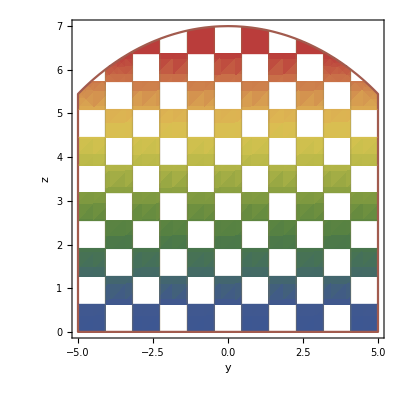

```mathematica
RegionPlot[z<Sqrt[49-((1300/1681)*(y^2))],{y,-5,5},{z,0,7},Mesh->10,MeshShading->{{Automatic,None},{None,Automatic}}, ColorFunction->"DarkRainbow",AxesLabel->{y,z}]
```

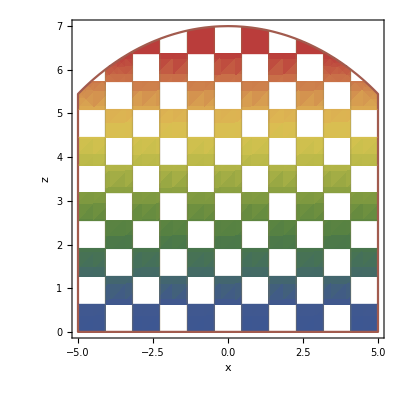

```mathematica
RegionPlot[z<Sqrt[49-((1300/1681)*(x^2))],{x,-5,5},{z,0,7},Mesh->10,MeshShading->{{Automatic,None},{None,Automatic}}, ColorFunction->"DarkRainbow",AxesLabel->{x,z}]
```

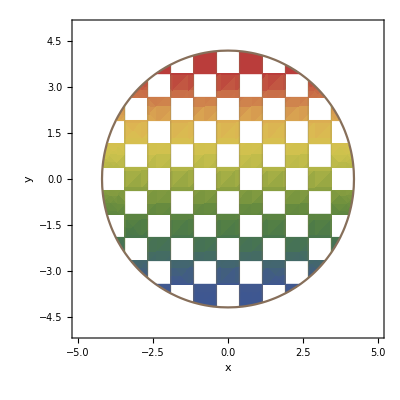

```mathematica
RegionPlot[x^2+y^2<4.2^2,{y,-5,5},{x,-5,5},Mesh->10,MeshShading->{{Automatic,None},{None,Automatic}}, ColorFunction->"DarkRainbow",AxesLabel->{x,y}]
```